Part::pkspec1: The expression x cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{0.29402,10.7042}

{19.8811,10.6763}

{17.8804,4.17816}

{10.2392,19.9053}

{4.26619,2.14013}

{0.360928,12.2269}

{1.12214,14.2264}

{12.8805,0.484283}

{0.48076,7.43444}

{0.55357,7.12062}

{7.28234,0.471634}

{15.1363,18.1812}

{16.0647,17.6175}

{8.86314,0.162721}

{12.5833,19.4852}

{19.4204,7.10511}

{0.840923,13.6441}

{3.2236,16.8941}

{19.5729,12.0623}

{10.6586,0.0819224}

{1.78407,4.58402}

{0.95657,13.9465}

{14.3824,1.14932}

{18.797,14.3049}

{6.49971,19.1477}

Part::pkspec1: The expression x cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{36.1733,37.8492}

{20.8378,33.8265}

{24.1016,37.7469}

{35.53,21.8241}

{33.7427,20.7929}

{37.6729,23.9238}

{20.7126,27.705}

{39.6917,31.3037}

{39.1671,33.5081}

{39.3994,27.259}

{27.6937,20.5169}

{20.5937,32.1935}

{29.5688,20.2073}

{22.5458,36.2275}

{26.1405,39.0395}

{20.4639,30.3498}

{22.1432,23.87}

{21.4679,35.1168}

{35.3165,38.2671}

{20.5721,28.7745}

{32.3891,38.9848}

{25.3725,21.3175}

{39.8268,29.2743}

{39.5669,27.7217}

{36.7045,37.1561}

{29.4773,39.3263}

{31.6755,20.4074}

{31.5171,39.1062}

{28.6765,39.3559}

{{6.49971,19.1477},{18.797,14.3049},{14.3824,1.14932},{0.95657,13.9465},{1.78407,4.58402},{10.6586,0.0819224},{19.5729,12.0623},{3.2236,16.8941},{0.840923,13.6441},{19.4204,7.10511},{12.5833,19.4852},{8.86314,0.162721},{16.0647,17.6175},{15.1363,18.1812},{7.28234,0.471634},{0.55357,7.12062},{0.48076,7.43444},{12.8805,0.484283},{1.12214,14.2264},{0.360928,12.2269},{4.26619,2.14013},{10.2392,19.9053},{17.8804,4.17816},{19.8811,10.6763},{0.29402,10.7042}}

{{28.6765,39.3559},{31.5171,39.1062},{31.6755,20.4074},{29.4773,39.3263},{36.7045,37.1561},{39.5669,27.7217},{39.8268,29.2743},{25.3725,21.3175},{32.3891,38.9848},{20.5721,28.7745},{35.3165,38.2671},{21.4679,35.1168},{22.1432,23.87},{20.4639,30.3498},{26.1405,39.0395},{22.5458,36.2275},{29.5688,20.2073},{20.5937,32.1935},{27.6937,20.5169},{39.3994,27.259},{39.1671,33.5081},{39.6917,31.3037},{20.7126,27.705},{37.6729,23.9238},{33.7427,20.7929},{35.53,21.8241},{24.1016,37.7469},{20.8378,33.8265},{36.1733,37.8492}}

{{16.0647,17.6175},{22.1432,23.87}}

{{16.0647,17.6175},{15.1363,18.1812}}

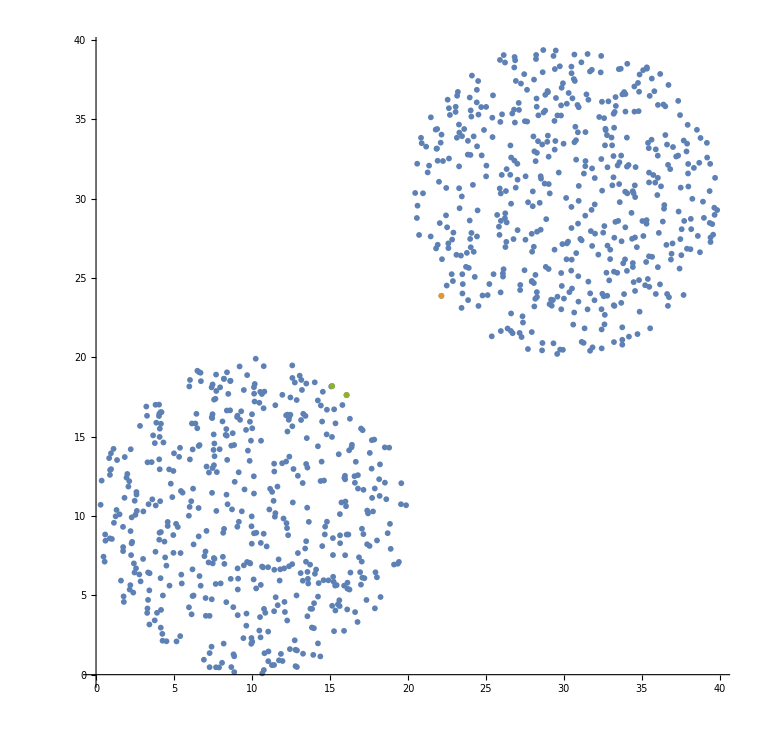

{{16.0647,17.6175},{22.1432,23.87}}

{{16.0647,17.6175},{15.7971,16.9903}}

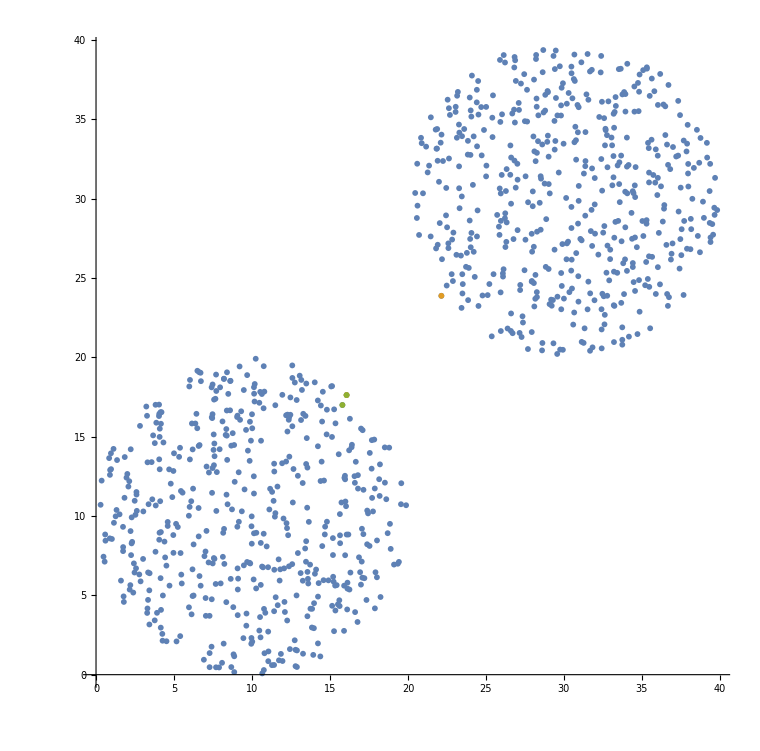

BODY JSOU STEJNE

```mathematica
(*Global Variables*)
numOfPoints = 500;

(*Distributin function for generating point on given region*)
RegionDistribution/:
Random`DistributionVector[RegionDistribution[reg_MeshRegion],n_Integer,prec_?Positive]:=Module[{d=RegionDimension@reg,cells,measures,s,m},cells=Developer`ToPackedArray@MeshPrimitives[reg,d][[All,1]];
s=RandomVariate[DirichletDistribution@ConstantArray[1,d+1],n];
measures=PropertyValue[{reg,d},MeshCellMeasure];
m=RandomVariate[#,n]&@EmpiricalDistribution[measures->Range@Length@cells];
#[[All,1]] (1-Total[s,{2}])+Total[#[[All,2;;]] s,{2}]&@cells[[m]]]

(*Initialize of two regions*)
region1 = DiscretizeRegion@Disk[{10,10},10];
region2 = DiscretizeRegion@Disk[{30, 30}, 10];
pts1= RandomVariate[RegionDistribution[region1],numOfPoints];
pts2= RandomVariate[RegionDistribution[region2],numOfPoints];

area = Join[pts1, pts2];

(*Exctract points on convex hull - both regions*)
convexHullpts1 = RegionBoundary[ConvexHullMesh[pts1]];
convexHullpts2 = RegionBoundary[ConvexHullMesh[pts2]];

arrayOneConvexHull = pts1;
cutConvexHull1[x_]=If[RegionMember[convexHullpts1,arrayOneConvexHull[[x]]],Print[arrayOneConvexHull[[x]]], arrayOneConvexHull = Delete[arrayOneConvexHull, x]];
For[i=numOfPoints, i>0, i--, cutConvexHull1[i]];

arrayTwoConvexHull = pts2;
cutConvexHull2[x_]=If[RegionMember[convexHullpts2,arrayTwoConvexHull[[x]]],Print[arrayTwoConvexHull[[x]]], arrayTwoConvexHull = Delete[arrayTwoConvexHull, x]];
For[i=numOfPoints, i>0, i--, cutConvexHull2[i]];

arrayOneConvexHull
arrayTwoConvexHull

(*Calculate nearest on ConvexHull*)
f = Nearest[arrayOneConvexHull];
c=Flatten[f/@arrayTwoConvexHull,1];
closestPairOnConvexHull = Flatten[Transpose[{c[[#]],arrayTwoConvexHull[[#]]}]&@Ordering[Norm/@(c-arrayTwoConvexHull),1],1]
transmittersOnConvexHull = Nearest[arrayOneConvexHull,closestPairOnConvexHull[[1]],{2,5}]
ListPlot[{area, closestPairOnConvexHull, transmittersOnConvexHull}, AspectRatio->Automatic]

(*Calculate nearest point of two regions*)
r = Nearest[pts1];
d = Flatten[r/@pts2,1];
closestPair = Flatten[Transpose[{d[[#]],pts2[[#]]}]&@Ordering[Norm/@(d-pts2),1],1]
transmitters = Nearest[pts1,closestPair[[1]],{2,2}]
ListPlot[{area, closestPair, transmitters}, AspectRatio->Automatic]

(*Check if points are the same and if they belong to convex hull*)
If[closestPair == closestPairOnConvexHull,
Print["BODY JSOU STEJNE"],
If[(ContainsAny[arrayOneConvexHull, closestPair])&&(ContainsAny[arrayTwoConvexHull, closestPair]),Print["BODY JSOU JINE ALE OBA NA KONVEXNÍ OBÁLCE"], 
Print["JEDEN NEBO OBA BODY NEJSOU NA KONVEXNÍ OBÁLCE"]]]


(*
(*Calculate nearest on ConvexHull*)
oneToTwoConvexHull = First[Nearest[arrayOneConvexHull,arrayTwoConvexHull]]
Nearest[arrayOneConvexHull,arrayTwoConvexHull]
twoToOneConvexHull = First[Nearest[arrayTwoConvexHull,arrayOneConvexHull]]
Nearest[arrayTwoConvexHull,arrayOneConvexHull]
ListPlot[{area, oneToTwoConvexHull, twoToOneConvexHull}, AspectRatio->Automatic]

(*Calculate nearest point of two regions*)
Nearest[pts1,pts2]
oneToTwo = First[Nearest[pts1,pts2]]
Nearest[pts2,pts1]
twoTo0ne= First[Nearest[pts2,pts1]]
ListPlot[{area, oneToTwo, twoTo0ne}, AspectRatio->Automatic]

(*Check if points are the same and if they belong to convex hull*)
If[(oneToTwo == oneToTwoConvexHull) && (twoTo0ne == twoToOneConvexHull),Print["BODY JSOU STEJNE"],
If[(ContainsAny[arrayOneConvexHull, oneToTwo])&&(ContainsAny[arrayTwoConvexHull, twoTo0ne]),Print["BODY JSOU JINE ALE OBA NA KONVEXNÍ OBÁLCE"]], Print["JEDEN NEBO OBA BODY NEJSOU NA KONVEXNÍ OBÁLCE"] ]*)
```